```mathematica
data= {{0.005,0.5},{0.007,0.6},{0.015,0.6},{0.02,0.7},{0.025,0.8},{0.03,0.8},{0.035,0.82},{0.04,0.85},{0.045,1},{0.05,1.1},{0.055,1.1},{0.07,1.2}}
```

{{0.005,0.5},{0.007,0.6},{0.015,0.6},{0.02,0.7},{0.025,0.8},{0.03,0.8},{0.035,0.82},{0.04,0.85},{0.045,1},{0.05,1.1},{0.055,1.1},{0.07,1.2}}

0.477245+10.9397 x

0.462606+12.1192 x-16.7199 x^2

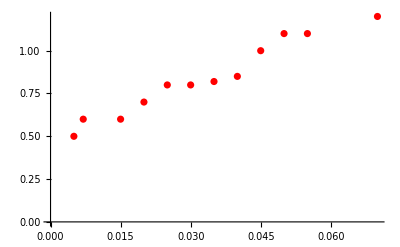

```mathematica
line = Fit[data,{1,x},x]
parabola = Fit[data,{1,x,x^2},x]
Show[ListPlot[data,PlotStyle->Red],Plot[{line,parabola},{x,9,10}]]
```

```mathematica
Trabajo realizado
```

```mathematica
Integrate[0.477+10.939 x,x]
```

0.477 x+5.4695 x^2

```mathematica
0.477*0.1+5.4695(0.1)^2
```

0.102395